# Minimal regulation network for value antagonism

In this section we analyse the following 8 networks to check which network can satisfy value antagonism-

The math is done using the following formulas--Graphics-

## Network A

The dynamics of A,B and M are-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, am] m-(Subscript[k, da]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-(Subscript[k, db]+Subscript[k, d1]*Subscript[s, 1])*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a+Subscript[k, mb]*b-(Subscript[k, dm]+Subscript[k, rm]*m)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→1/(-k_da-k_d2 s_2)(-k_a0-(k_am k_da k_db k_dm)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))+(k_am^2 k_db k_ma)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am k_d1 k_da k_dm s_1)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))+(k_am^2 k_d1 k_ma s_1)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am k_d2 k_db k_dm s_2)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am k_d1 k_d2 k_dm s_1 s_2)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))+(k_am √((-k_da k_db k_dm+k_am k_db k_ma-k_d1 k_da k_dm s_1+k_am k_d1 k_ma s_1-k_d2 k_db k_dm s_2-k_d1 k_d2 k_dm s_1 s_2)^2-4 (k_da k_db k_m0+k_a0 k_db k_ma+k_b0 k_da k_mb+k_d1 k_da k_m0 s_1+k_a0 k_d1 k_ma s_1+k_d2 k_db k_m0 s_2+k_b0 k_d2 k_mb s_2+k_d1 k_d2 k_m0 s_1 s_2) (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2)))/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))),b→k_b0/(k_db+k_d1 s_1),m→(k_da k_db k_dm-k_am k_db k_ma+k_d1 k_da k_dm s_1-k_am k_d1 k_ma s_1+k_d2 k_db k_dm s_2+k_d1 k_d2 k_dm s_1 s_2-√((-k_da k_db k_dm+k_am k_db k_ma-k_d1 k_da k_dm s_1+k_am k_d1 k_ma s_1-k_d2 k_db k_dm s_2-k_d1 k_d2 k_dm s_1 s_2)^2-4 (k_da k_db k_m0+k_a0 k_db k_ma+k_b0 k_da k_mb+k_d1 k_da k_m0 s_1+k_a0 k_d1 k_ma s_1+k_d2 k_db k_m0 s_2+k_b0 k_d2 k_mb s_2+k_d1 k_d2 k_m0 s_1 s_2) (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2)))/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))},{a→1/(-k_da-k_d2 s_2)(-k_a0-(k_am k_da k_db k_dm)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))+(k_am^2 k_db k_ma)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am k_d1 k_da k_dm s_1)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))+(k_am^2 k_d1 k_ma s_1)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am k_d2 k_db k_dm s_2)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am k_d1 k_d2 k_dm s_1 s_2)/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))-(k_am √((-k_da k_db k_dm+k_am k_db k_ma-k_d1 k_da k_dm s_1+k_am k_d1 k_ma s_1-k_d2 k_db k_dm s_2-k_d1 k_d2 k_dm s_1 s_2)^2-4 (k_da k_db k_m0+k_a0 k_db k_ma+k_b0 k_da k_mb+k_d1 k_da k_m0 s_1+k_a0 k_d1 k_ma s_1+k_d2 k_db k_m0 s_2+k_b0 k_d2 k_mb s_2+k_d1 k_d2 k_m0 s_1 s_2) (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2)))/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))),b→k_b0/(k_db+k_d1 s_1),m→(k_da k_db k_dm-k_am k_db k_ma+k_d1 k_da k_dm s_1-k_am k_d1 k_ma s_1+k_d2 k_db k_dm s_2+k_d1 k_d2 k_dm s_1 s_2+√((-k_da k_db k_dm+k_am k_db k_ma-k_d1 k_da k_dm s_1+k_am k_d1 k_ma s_1-k_d2 k_db k_dm s_2-k_d1 k_d2 k_dm s_1 s_2)^2-4 (k_da k_db k_m0+k_a0 k_db k_ma+k_b0 k_da k_mb+k_d1 k_da k_m0 s_1+k_a0 k_d1 k_ma s_1+k_d2 k_db k_m0 s_2+k_b0 k_d2 k_mb s_2+k_d1 k_d2 k_m0 s_1 s_2) (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2)))/(2 (-k_da k_db k_rm-k_d1 k_da k_rm s_1-k_d2 k_db k_rm s_2-k_d1 k_d2 k_rm s_1 s_2))}}

### For plotting we set all parameters to 1.

```mathematica
dadt=1+m-(1+Subscript[s, 2])*a;
dbdt=1-(1+Subscript[s, 1])*b;
dmdt=1+a+b-(1+m)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(-1+s_2/(2 (1+s_1+s_2+s_1 s_2))+(s_1 s_2)/(2 (1+s_1+s_2+s_1 s_2))+(√(1+s_1) √(12+8 s_1+20 s_2+12 s_1 s_2+9 s_2^2+5 s_1 s_2^2))/(2 (1+s_1+s_2+s_1 s_2)))/(-1-s_2),b→1/(1+s_1),m→(-s_2-s_1 s_2-√(1+s_1) √(12+8 s_1+20 s_2+12 s_1 s_2+9 s_2^2+5 s_1 s_2^2))/(2 (1+s_1+s_2+s_1 s_2))},{a→(-1+s_2/(2 (1+s_1+s_2+s_1 s_2))+(s_1 s_2)/(2 (1+s_1+s_2+s_1 s_2))-(√(1+s_1) √(12+8 s_1+20 s_2+12 s_1 s_2+9 s_2^2+5 s_1 s_2^2))/(2 (1+s_1+s_2+s_1 s_2)))/(-1-s_2),b→1/(1+s_1),m→(-s_2-s_1 s_2+√(1+s_1) √(12+8 s_1+20 s_2+12 s_1 s_2+9 s_2^2+5 s_1 s_2^2))/(2 (1+s_1+s_2+s_1 s_2))}}

Expressions and surface map in steady state-

```mathematica
aP=(-1+Subscript[s, 2]/(2 (1+Subscript[s, 1]+Subscript[s, 2]+Subscript[s, 1] Subscript[s, 2]))+(Subscript[s, 1] Subscript[s, 2])/(2 (1+Subscript[s, 1]+Subscript[s, 2]+Subscript[s, 1] Subscript[s, 2]))-(√(1+Subscript[s, 1]) √(12+8 Subscript[s, 1]+20 Subscript[s, 2]+12 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2+5 Subscript[s, 1] Subscript[s, 2]^2))/(2 (1+Subscript[s, 1]+Subscript[s, 2]+Subscript[s, 1] Subscript[s, 2])))/(-1-Subscript[s, 2]);
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

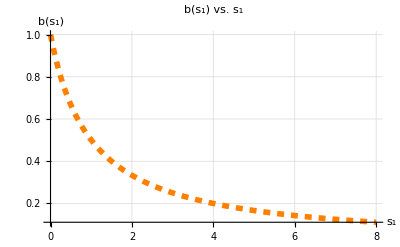

```mathematica
bp=1/(1+Subscript[s, 1]);
plotset={PlotStyle->Thick,AxesStyle->Thick,FrameStyle->Thick, TicksStyle->Directive[Black,15]};
Plot[bp,{Subscript[s, 1],0,8}, 
AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["b(s_1)",Bold,20,FontColor->Black]},
PlotLabel->Style["b(s_1) vs. s_1",Bold,30,FontColor->Black],
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.01]},Evaluate@plotset]
```

```mathematica
mP=(-Subscript[s, 2]-Subscript[s, 1] Subscript[s, 2]+√(1+Subscript[s, 1]) √(12+8 Subscript[s, 1]+20 Subscript[s, 2]+12 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2+5 Subscript[s, 1] Subscript[s, 2]^2))/(2 (1+Subscript[s, 1]+Subscript[s, 2]+Subscript[s, 1] Subscript[s, 2]));
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network A fails.

## Network B

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, aa]*a-(Subscript[k, da]+Subscript[k, d1]*Subscript[s, 1]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-(Subscript[k, db]+Subscript[k, bb]*b)*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a-(Subscript[k, dm]+Subscript[k, mb]*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→k_a0/(-k_aa+k_da+k_d1 s_1+k_d2 s_2),b→-(k_db-√(4 k_b0 k_bb+k_db^2))/(2 k_bb),m→(-2 k_aa k_bb k_dm k_m0+2 k_bb k_da k_dm k_m0+2 k_a0 k_bb k_dm k_ma+k_aa k_db k_m0 k_mb-k_da k_db k_m0 k_mb+k_aa √(4 k_b0 k_bb+k_db^2) k_m0 k_mb-k_da √(4 k_b0 k_bb+k_db^2) k_m0 k_mb-k_a0 k_db k_ma k_mb-k_a0 √(4 k_b0 k_bb+k_db^2) k_ma k_mb+2 k_bb k_d1 k_dm k_m0 s_1-k_d1 k_db k_m0 k_mb s_1-k_d1 √(4 k_b0 k_bb+k_db^2) k_m0 k_mb s_1+2 k_bb k_d2 k_dm k_m0 s_2-k_d2 k_db k_m0 k_mb s_2-k_d2 √(4 k_b0 k_bb+k_db^2) k_m0 k_mb s_2)/(2 (-k_aa k_bb k_dm^2+k_bb k_da k_dm^2+k_aa k_db k_dm k_mb-k_da k_db k_dm k_mb+k_aa k_b0 k_mb^2-k_b0 k_da k_mb^2+k_bb k_d1 k_dm^2 s_1-k_d1 k_db k_dm k_mb s_1-k_b0 k_d1 k_mb^2 s_1+k_bb k_d2 k_dm^2 s_2-k_d2 k_db k_dm k_mb s_2-k_b0 k_d2 k_mb^2 s_2))},{a→k_a0/(-k_aa+k_da+k_d1 s_1+k_d2 s_2),b→-(k_db+√(4 k_b0 k_bb+k_db^2))/(2 k_bb),m→(-2 k_aa k_bb k_dm k_m0+2 k_bb k_da k_dm k_m0+2 k_a0 k_bb k_dm k_ma+k_aa k_db k_m0 k_mb-k_da k_db k_m0 k_mb-k_aa √(4 k_b0 k_bb+k_db^2) k_m0 k_mb+k_da √(4 k_b0 k_bb+k_db^2) k_m0 k_mb-k_a0 k_db k_ma k_mb+k_a0 √(4 k_b0 k_bb+k_db^2) k_ma k_mb+2 k_bb k_d1 k_dm k_m0 s_1-k_d1 k_db k_m0 k_mb s_1+k_d1 √(4 k_b0 k_bb+k_db^2) k_m0 k_mb s_1+2 k_bb k_d2 k_dm k_m0 s_2-k_d2 k_db k_m0 k_mb s_2+k_d2 √(4 k_b0 k_bb+k_db^2) k_m0 k_mb s_2)/(2 (-k_aa k_bb k_dm^2+k_bb k_da k_dm^2+k_aa k_db k_dm k_mb-k_da k_db k_dm k_mb+k_aa k_b0 k_mb^2-k_b0 k_da k_mb^2+k_bb k_d1 k_dm^2 s_1-k_d1 k_db k_dm k_mb s_1-k_b0 k_d1 k_mb^2 s_1+k_bb k_d2 k_dm^2 s_2-k_d2 k_db k_dm k_mb s_2-k_b0 k_d2 k_mb^2 s_2))}}

### For plotting we set all parameters to 1.

```mathematica
dadt=1+1*a-(2+1*Subscript[s, 1]+1*Subscript[s, 2])*a;
dbdt=1-(1+1*b)*b;
dmdt=1+1*a-(1+1*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→1/(1+s_1+s_2),b→1/2 (-1-√5),m→(-2-2 √5-s_1-√5 s_1-s_2-√5 s_2)/(2 (1+s_1+s_2))},{a→1/(1+s_1+s_2),b→1/2 (-1+√5),m→(-2+2 √5-s_1+√5 s_1-s_2+√5 s_2)/(2 (1+s_1+s_2))}}

Expressions in steady states and surface maps-

```mathematica
aP=1/(1+Subscript[s, 1]+Subscript[s, 2]);
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

b is constant.

```mathematica
mP=(-2+2 √5-Subscript[s, 1]+√5 Subscript[s, 1]-Subscript[s, 2]+√5 Subscript[s, 2])/(2 (1+Subscript[s, 1]+Subscript[s, 2]));
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network B fails.

## Network C

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, ab]*b-(Subscript[k, da]+Subscript[k, d1]*Subscript[s, 1]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-(Subscript[k, db]+Subscript[k, rb]*b)*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a-(Subscript[k, dm]+Subscript[k, mb]*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(2 k_a0-(k_ab k_db)/k_rb+(k_ab √(k_db^2+4 k_b0 k_rb))/k_rb)/(2 (k_da+k_d1 s_1+k_d2 s_2)),b→-(k_db-√(k_db^2+4 k_b0 k_rb))/(2 k_rb),m→(k_ab k_db k_dm k_ma+k_da k_db k_m0 k_mb+2 k_ab k_b0 k_ma k_mb+k_a0 k_db k_ma k_mb-2 k_da k_dm k_m0 k_rb-2 k_a0 k_dm k_ma k_rb-k_ab k_dm k_ma √(k_db^2+4 k_b0 k_rb)+k_da k_m0 k_mb √(k_db^2+4 k_b0 k_rb)+k_a0 k_ma k_mb √(k_db^2+4 k_b0 k_rb)+k_d1 k_db k_m0 k_mb s_1-2 k_d1 k_dm k_m0 k_rb s_1+k_d1 k_m0 k_mb √(k_db^2+4 k_b0 k_rb) s_1+k_d2 k_db k_m0 k_mb s_2-2 k_d2 k_dm k_m0 k_rb s_2+k_d2 k_m0 k_mb √(k_db^2+4 k_b0 k_rb) s_2)/(2 (k_da k_db k_dm k_mb+k_b0 k_da k_mb^2-k_da k_dm^2 k_rb+k_d1 k_db k_dm k_mb s_1+k_b0 k_d1 k_mb^2 s_1-k_d1 k_dm^2 k_rb s_1+k_d2 k_db k_dm k_mb s_2+k_b0 k_d2 k_mb^2 s_2-k_d2 k_dm^2 k_rb s_2))},{a→(2 k_a0-(k_ab k_db)/k_rb-(k_ab √(k_db^2+4 k_b0 k_rb))/k_rb)/(2 (k_da+k_d1 s_1+k_d2 s_2)),b→-(k_db+√(k_db^2+4 k_b0 k_rb))/(2 k_rb),m→(k_ab k_db k_dm k_ma+k_da k_db k_m0 k_mb+2 k_ab k_b0 k_ma k_mb+k_a0 k_db k_ma k_mb-2 k_da k_dm k_m0 k_rb-2 k_a0 k_dm k_ma k_rb+k_ab k_dm k_ma √(k_db^2+4 k_b0 k_rb)-k_da k_m0 k_mb √(k_db^2+4 k_b0 k_rb)-k_a0 k_ma k_mb √(k_db^2+4 k_b0 k_rb)+k_d1 k_db k_m0 k_mb s_1-2 k_d1 k_dm k_m0 k_rb s_1-k_d1 k_m0 k_mb √(k_db^2+4 k_b0 k_rb) s_1+k_d2 k_db k_m0 k_mb s_2-2 k_d2 k_dm k_m0 k_rb s_2-k_d2 k_m0 k_mb √(k_db^2+4 k_b0 k_rb) s_2)/(2 (k_da k_db k_dm k_mb+k_b0 k_da k_mb^2-k_da k_dm^2 k_rb+k_d1 k_db k_dm k_mb s_1+k_b0 k_d1 k_mb^2 s_1-k_d1 k_dm^2 k_rb s_1+k_d2 k_db k_dm k_mb s_2+k_b0 k_d2 k_mb^2 s_2-k_d2 k_dm^2 k_rb s_2))}}

### For plotting we set all parameters to 1.

```mathematica
dadt=1+1*b-(1+1*Subscript[s, 1]+1*Subscript[s, 2])*a;
dbdt=1-(1+1*b)*b;
dmdt=1+1*a-(1+1*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(1-√5)/(2 (1+s_1+s_2)),b→1/2 (-1-√5),m→(1-√5-s_1-√5 s_1-s_2-√5 s_2)/(2 (1+s_1+s_2))},{a→(1+√5)/(2 (1+s_1+s_2)),b→1/2 (-1+√5),m→(1+√5-s_1+√5 s_1-s_2+√5 s_2)/(2 (1+s_1+s_2))}}

Steady state values and surface plots-

```mathematica
aP=(1+√5)/(2 (1+Subscript[s, 1]+Subscript[s, 2]));
Plot3D[aPC,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

b is a constant.

```mathematica
mP=(1+√5-Subscript[s, 1]+√5 Subscript[s, 1]-Subscript[s, 2]+√5 Subscript[s, 2])/(2 (1+Subscript[s, 1]+Subscript[s, 2]));
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network C fails.

## Network D

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, aa]*a-(Subscript[k, da]+Subscript[k, d1]*Subscript[s, 1]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-(Subscript[k, db]+Subscript[k, rb]*a)*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a-(Subscript[k, dm]+Subscript[k, mb]*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→k_a0/(-k_aa+k_da+k_d1 s_1+k_d2 s_2),b→(k_b0 (k_aa-k_da-k_d1 s_1-k_d2 s_2))/(k_aa k_db-k_da k_db-k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2),m→((k_aa k_db-k_da k_db-k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2) (k_aa k_m0-k_da k_m0-k_a0 k_ma-k_d1 k_m0 s_1-k_d2 k_m0 s_2))/((k_aa-k_da-k_d1 s_1-k_d2 s_2) (k_aa k_db k_dm-k_da k_db k_dm+k_aa k_b0 k_mb-k_b0 k_da k_mb-k_a0 k_dm k_rb-k_d1 k_db k_dm s_1-k_b0 k_d1 k_mb s_1-k_d2 k_db k_dm s_2-k_b0 k_d2 k_mb s_2))}}

### For plotting we set all parameters to 1.

```mathematica
dadt=1+1*a-(2+1*Subscript[s, 1]+1*Subscript[s, 2])*a;
dbdt=1-(1+1*a)*b;
dmdt=1+1*a-(1+1*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→1/(1+s_1+s_2),b→(1+s_1+s_2)/(2+s_1+s_2),m→(2+s_1+s_2)^2/(3+5 s_1+2 s_1^2+5 s_2+4 s_1 s_2+2 s_2^2)}}

Steady state values and surface plots-

```mathematica
aP=1/(1+Subscript[s, 1]+Subscript[s, 2]);
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
bP=(1+Subscript[s, 1]+Subscript[s, 2])/(2+Subscript[s, 1]+Subscript[s, 2]);
Plot3D[bP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["b(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["b(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
mP=(2+Subscript[s, 1]+Subscript[s, 2])^2/(3+5 Subscript[s, 1]+2 Subscript[s, 1]^2+5 Subscript[s, 2]+4 Subscript[s, 1] Subscript[s, 2]+2 Subscript[s, 2]^2);
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network D fails.

## Network E

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, ab]*b-(Subscript[k, da]+Subscript[k, d1]*Subscript[s, 1]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-(Subscript[k, db]+Subscript[k, rb]*a)*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a-(Subscript[k, dm]+Subscript[k, mb]*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(k_da k_db-k_a0 k_rb+k_d1 k_db s_1+k_d2 k_db s_2-√((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)),b→1/k_ab(-k_a0+(k_da^2 k_db)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_da k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1 k_da k_db s_1)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d1 k_rb s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1^2 k_db s_1^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d2 k_da k_db s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d2 k_rb s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1 k_d2 k_db s_1 s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)+(k_d2^2 k_db s_2^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_da √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1 s_1 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d2 s_2 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))),m→(-k_da k_db k_m0 k_mb-k_ab k_b0 k_ma k_mb-k_a0 k_db k_ma k_mb+k_ab k_dm k_m0 k_rb-k_d1 k_db k_m0 k_mb s_1-k_d2 k_db k_m0 k_mb s_2+(k_ab k_da k_db k_dm k_ma k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_da^2 k_db k_m0 k_mb k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_da k_db k_ma k_mb k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_ab k_dm k_ma k_rb^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_da k_m0 k_mb k_rb^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0^2 k_ma k_mb k_rb^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_ab k_d1 k_db k_dm k_ma k_rb s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1 k_da k_db k_m0 k_mb k_rb s_1)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d1 k_db k_ma k_mb k_rb s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_d1 k_m0 k_mb k_rb^2 s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1^2 k_db k_m0 k_mb k_rb s_1^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_ab k_d2 k_db k_dm k_ma k_rb s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d2 k_da k_db k_m0 k_mb k_rb s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d2 k_db k_ma k_mb k_rb s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_d2 k_m0 k_mb k_rb^2 s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1 k_d2 k_db k_m0 k_mb k_rb s_1 s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_d2^2 k_db k_m0 k_mb k_rb s_2^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_ab k_dm k_ma k_rb √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_da k_m0 k_mb k_rb √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_ma k_mb k_rb √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1 k_m0 k_mb k_rb s_1 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d2 k_m0 k_mb k_rb s_2 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(-k_da k_db k_dm k_mb-k_b0 k_da k_mb^2+k_ab k_dm^2 k_rb-k_a0 k_dm k_mb k_rb-k_d1 k_db k_dm k_mb s_1-k_b0 k_d1 k_mb^2 s_1-k_d2 k_db k_dm k_mb s_2-k_b0 k_d2 k_mb^2 s_2)},{a→(k_da k_db-k_a0 k_rb+k_d1 k_db s_1+k_d2 k_db s_2+√((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)),b→1/k_ab(-k_a0+(k_da^2 k_db)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_da k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1 k_da k_db s_1)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d1 k_rb s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1^2 k_db s_1^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d2 k_da k_db s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d2 k_rb s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1 k_d2 k_db s_1 s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)+(k_d2^2 k_db s_2^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_da √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d1 s_1 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_d2 s_2 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))),m→(-k_da k_db k_m0 k_mb-k_ab k_b0 k_ma k_mb-k_a0 k_db k_ma k_mb+k_ab k_dm k_m0 k_rb-k_d1 k_db k_m0 k_mb s_1-k_d2 k_db k_m0 k_mb s_2+(k_ab k_da k_db k_dm k_ma k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_da^2 k_db k_m0 k_mb k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_da k_db k_ma k_mb k_rb)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_ab k_dm k_ma k_rb^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_da k_m0 k_mb k_rb^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0^2 k_ma k_mb k_rb^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_ab k_d1 k_db k_dm k_ma k_rb s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1 k_da k_db k_m0 k_mb k_rb s_1)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d1 k_db k_ma k_mb k_rb s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_d1 k_m0 k_mb k_rb^2 s_1)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1^2 k_db k_m0 k_mb k_rb s_1^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_ab k_d2 k_db k_dm k_ma k_rb s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d2 k_da k_db k_m0 k_mb k_rb s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_a0 k_d2 k_db k_ma k_mb k_rb s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_a0 k_d2 k_m0 k_mb k_rb^2 s_2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1 k_d2 k_db k_m0 k_mb k_rb s_1 s_2)/(-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)-(k_d2^2 k_db k_m0 k_mb k_rb s_2^2)/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))+(k_ab k_dm k_ma k_rb √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_da k_m0 k_mb k_rb √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_a0 k_ma k_mb k_rb √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d1 k_m0 k_mb k_rb s_1 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2))-(k_d2 k_m0 k_mb k_rb s_2 √((-k_da k_db+k_a0 k_rb-k_d1 k_db s_1-k_d2 k_db s_2)^2-4 (k_ab k_b0+k_a0 k_db) (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(2 (-k_da k_rb-k_d1 k_rb s_1-k_d2 k_rb s_2)))/(-k_da k_db k_dm k_mb-k_b0 k_da k_mb^2+k_ab k_dm^2 k_rb-k_a0 k_dm k_mb k_rb-k_d1 k_db k_dm k_mb s_1-k_b0 k_d1 k_mb^2 s_1-k_d2 k_db k_dm k_mb s_2-k_b0 k_d2 k_mb^2 s_2)}}

### For plotting-

```mathematica
dadt=1+1*b-(1+1*Subscript[s, 1]+1*Subscript[s, 2])*a;
dbdt=1-(1+1*a)*b;
dmdt=1+1*a-(1+1*b)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(-s_1-s_2-√((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2)),b→-1-s_1/(2 (1+s_1+s_2))-s_1^2/(2 (1+s_1+s_2))-s_2/(2 (1+s_1+s_2))-(s_1 s_2)/(1+s_1+s_2)-s_2^2/(2 (1+s_1+s_2))-(√((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))-(s_1 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))-(s_2 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2)),m→(2+s_1+s_2-s_1/(2 (1+s_1+s_2))-s_1^2/(2 (1+s_1+s_2))-s_2/(2 (1+s_1+s_2))-(s_1 s_2)/(1+s_1+s_2)-s_2^2/(2 (1+s_1+s_2))-(√((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))-(s_1 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))-(s_2 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2)))/(2+2 s_1+2 s_2)},{a→(-s_1-s_2+√((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2)),b→-1-s_1/(2 (1+s_1+s_2))-s_1^2/(2 (1+s_1+s_2))-s_2/(2 (1+s_1+s_2))-(s_1 s_2)/(1+s_1+s_2)-s_2^2/(2 (1+s_1+s_2))+(√((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))+(s_1 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))+(s_2 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2)),m→(2+s_1+s_2-s_1/(2 (1+s_1+s_2))-s_1^2/(2 (1+s_1+s_2))-s_2/(2 (1+s_1+s_2))-(s_1 s_2)/(1+s_1+s_2)-s_2^2/(2 (1+s_1+s_2))+(√((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))+(s_1 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2))+(s_2 √((s_1+s_2)^2+8 (1+s_1+s_2)))/(2 (1+s_1+s_2)))/(2+2 s_1+2 s_2)}}

Surface plots-

```mathematica
aP=(-Subscript[s, 1]-Subscript[s, 2]+√((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2]));
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
bP=-1-Subscript[s, 1]/(2 (1+Subscript[s, 1]+Subscript[s, 2]))-Subscript[s, 1]^2/(2 (1+Subscript[s, 1]+Subscript[s, 2]))-Subscript[s, 2]/(2 (1+Subscript[s, 1]+Subscript[s, 2]))-(Subscript[s, 1] Subscript[s, 2])/(1+Subscript[s, 1]+Subscript[s, 2])-Subscript[s, 2]^2/(2 (1+Subscript[s, 1]+Subscript[s, 2]))+(√((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2]))+(Subscript[s, 1] √((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2]))+(Subscript[s, 2] √((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2]));
Plot3D[bP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["b(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["b(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
mP=(2+Subscript[s, 1]+Subscript[s, 2]-Subscript[s, 1]/(2 (1+Subscript[s, 1]+Subscript[s, 2]))-Subscript[s, 1]^2/(2 (1+Subscript[s, 1]+Subscript[s, 2]))-Subscript[s, 2]/(2 (1+Subscript[s, 1]+Subscript[s, 2]))-(Subscript[s, 1] Subscript[s, 2])/(1+Subscript[s, 1]+Subscript[s, 2])-Subscript[s, 2]^2/(2 (1+Subscript[s, 1]+Subscript[s, 2]))+(√((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2]))+(Subscript[s, 1] √((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2]))+(Subscript[s, 2] √((Subscript[s, 1]+Subscript[s, 2])^2+8 (1+Subscript[s, 1]+Subscript[s, 2])))/(2 (1+Subscript[s, 1]+Subscript[s, 2])))/(2+2 Subscript[s, 1]+2 Subscript[s, 2]);
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network E fails.

## Network F

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, am]*m-(Subscript[k, da]+Subscript[k, d1]*Subscript[s, 1]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-Subscript[k, db]*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a+Subscript[k, mb]*b-(Subscript[k, dm]+Subscript[k, mm]*m)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(-k_am k_da k_db k_dm+k_am^2 k_db k_ma+2 k_a0 k_da k_db k_mm-k_am k_d1 k_db k_dm s_1+2 k_a0 k_d1 k_db k_mm s_1-k_am k_d2 k_db k_dm s_2+2 k_a0 k_d2 k_db k_mm s_2-√((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)),b→k_b0/k_db,m→1/k_am(-k_a0-(k_am k_da^2 k_db k_dm)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_am^2 k_da k_db k_ma)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_a0 k_da^2 k_db k_mm)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d1 k_da k_db k_dm s_1)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(k_am^2 k_d1 k_db k_ma s_1)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(2 k_a0 k_d1 k_da k_db k_mm s_1)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d1^2 k_db k_dm s_1^2)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_a0 k_d1^2 k_db k_mm s_1^2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d2 k_da k_db k_dm s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(k_am^2 k_d2 k_db k_ma s_2)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(2 k_a0 k_d2 k_da k_db k_mm s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d1 k_d2 k_db k_dm s_1 s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(2 k_a0 k_d1 k_d2 k_db k_mm s_1 s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d2^2 k_db k_dm s_2^2)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_a0 k_d2^2 k_db k_mm s_2^2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_da √((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))-(k_d1 s_1 √((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))-(k_d2 s_2 √((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))},{a→(-k_am k_da k_db k_dm+k_am^2 k_db k_ma+2 k_a0 k_da k_db k_mm-k_am k_d1 k_db k_dm s_1+2 k_a0 k_d1 k_db k_mm s_1-k_am k_d2 k_db k_dm s_2+2 k_a0 k_d2 k_db k_mm s_2+√((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)),b→k_b0/k_db,m→1/k_am(-k_a0-(k_am k_da^2 k_db k_dm)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_am^2 k_da k_db k_ma)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_a0 k_da^2 k_db k_mm)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d1 k_da k_db k_dm s_1)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(k_am^2 k_d1 k_db k_ma s_1)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(2 k_a0 k_d1 k_da k_db k_mm s_1)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d1^2 k_db k_dm s_1^2)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_a0 k_d1^2 k_db k_mm s_1^2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d2 k_da k_db k_dm s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(k_am^2 k_d2 k_db k_ma s_2)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(2 k_a0 k_d2 k_da k_db k_mm s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d1 k_d2 k_db k_dm s_1 s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(2 k_a0 k_d1 k_d2 k_db k_mm s_1 s_2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)-(k_am k_d2^2 k_db k_dm s_2^2)/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_a0 k_d2^2 k_db k_mm s_2^2)/(k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)+(k_da √((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_d1 s_1 √((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2))+(k_d2 s_2 √((k_am k_da k_db k_dm-k_am^2 k_db k_ma-2 k_a0 k_da k_db k_mm+k_am k_d1 k_db k_dm s_1-2 k_a0 k_d1 k_db k_mm s_1+k_am k_d2 k_db k_dm s_2-2 k_a0 k_d2 k_db k_mm s_2)^2-4 (-k_a0 k_am k_db k_dm-k_am^2 k_db k_m0-k_am^2 k_b0 k_mb+k_a0^2 k_db k_mm) (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))/(2 (k_da^2 k_db k_mm+2 k_d1 k_da k_db k_mm s_1+k_d1^2 k_db k_mm s_1^2+2 k_d2 k_da k_db k_mm s_2+2 k_d1 k_d2 k_db k_mm s_1 s_2+k_d2^2 k_db k_mm s_2^2)))}}

### For plotting-

```mathematica
dadt=1+1*m-(1+1*Subscript[s, 1]+1*Subscript[s, 2])*a;
dbdt=1-1*b;
dmdt=1+1*a+1*b-(1+1*m)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→(2+s_1+s_2-√(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2)),b→1,m→-1+1/(1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2)+(3 s_1)/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+s_1^2/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(3 s_2)/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(s_1 s_2)/(1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2)+s_2^2/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))-(√(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))-(s_1 √(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))-(s_2 √(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))},{a→(2+s_1+s_2+√(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2)),b→1,m→-1+1/(1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2)+(3 s_1)/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+s_1^2/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(3 s_2)/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(s_1 s_2)/(1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2)+s_2^2/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(√(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(s_1 √(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))+(s_2 √(12+20 s_1+9 s_1^2+20 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+2 s_1+s_1^2+2 s_2+2 s_1 s_2+s_2^2))}}

Surface maps-

```mathematica
aP=(2+Subscript[s, 1]+Subscript[s, 2]+√(12+20 Subscript[s, 1]+9 Subscript[s, 1]^2+20 Subscript[s, 2]+18 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2))/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2));
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

b is constant.

```mathematica
mP=-1+1/(1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2)+(3 Subscript[s, 1])/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2))+Subscript[s, 1]^2/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2))+(3 Subscript[s, 2])/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2))+(Subscript[s, 1] Subscript[s, 2])/(1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2)+Subscript[s, 2]^2/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2))+(√(12+20 Subscript[s, 1]+9 Subscript[s, 1]^2+20 Subscript[s, 2]+18 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2))/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2))+(Subscript[s, 1] √(12+20 Subscript[s, 1]+9 Subscript[s, 1]^2+20 Subscript[s, 2]+18 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2))/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2))+(Subscript[s, 2] √(12+20 Subscript[s, 1]+9 Subscript[s, 1]^2+20 Subscript[s, 2]+18 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2))/(2 (1+2 Subscript[s, 1]+Subscript[s, 1]^2+2 Subscript[s, 2]+2 Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2));
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network F fails.

## Network G

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, aa]*a-(Subscript[k, da]+Subscript[k, d1]*Subscript[s, 1]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]-Subscript[k, db]*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a+Subscript[k, mb]*b-(Subscript[k, dm]+Subscript[k, mm]*m)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→k_a0/(-k_aa+k_da+k_d1 s_1+k_d2 s_2),b→k_b0/k_db,m→(k_aa k_db k_dm-k_da k_db k_dm-k_d1 k_db k_dm s_1-k_d2 k_db k_dm s_2-√((-k_aa k_db k_dm+k_da k_db k_dm+k_d1 k_db k_dm s_1+k_d2 k_db k_dm s_2)^2-4 (k_aa k_db k_m0-k_da k_db k_m0-k_a0 k_db k_ma+k_aa k_b0 k_mb-k_b0 k_da k_mb-k_d1 k_db k_m0 s_1-k_b0 k_d1 k_mb s_1-k_d2 k_db k_m0 s_2-k_b0 k_d2 k_mb s_2) (-k_aa k_db k_mm+k_da k_db k_mm+k_d1 k_db k_mm s_1+k_d2 k_db k_mm s_2)))/(2 (-k_aa k_db k_mm+k_da k_db k_mm+k_d1 k_db k_mm s_1+k_d2 k_db k_mm s_2))},{a→k_a0/(-k_aa+k_da+k_d1 s_1+k_d2 s_2),b→k_b0/k_db,m→(k_aa k_db k_dm-k_da k_db k_dm-k_d1 k_db k_dm s_1-k_d2 k_db k_dm s_2+√((-k_aa k_db k_dm+k_da k_db k_dm+k_d1 k_db k_dm s_1+k_d2 k_db k_dm s_2)^2-4 (k_aa k_db k_m0-k_da k_db k_m0-k_a0 k_db k_ma+k_aa k_b0 k_mb-k_b0 k_da k_mb-k_d1 k_db k_m0 s_1-k_b0 k_d1 k_mb s_1-k_d2 k_db k_m0 s_2-k_b0 k_d2 k_mb s_2) (-k_aa k_db k_mm+k_da k_db k_mm+k_d1 k_db k_mm s_1+k_d2 k_db k_mm s_2)))/(2 (-k_aa k_db k_mm+k_da k_db k_mm+k_d1 k_db k_mm s_1+k_d2 k_db k_mm s_2))}}

### For plotting-

```mathematica
dadt=1+1*a-(2+1*Subscript[s, 1]+1*Subscript[s, 2])*a;
dbdt=1-1*b;
dmdt=1+1*a+1*b-(1+1*m)*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→1/(1+s_1+s_2),b→1,m→(-1-s_1-s_2-√(13+22 s_1+9 s_1^2+22 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+s_1+s_2))},{a→1/(1+s_1+s_2),b→1,m→(-1-s_1-s_2+√(13+22 s_1+9 s_1^2+22 s_2+18 s_1 s_2+9 s_2^2))/(2 (1+s_1+s_2))}}

Surface maps-

```mathematica
aP=1/(1+Subscript[s, 1]+Subscript[s, 2]);
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

b is constant.

```mathematica
mP=(-1-Subscript[s, 1]-Subscript[s, 2]+√(13+22 Subscript[s, 1]+9 Subscript[s, 1]^2+22 Subscript[s, 2]+18 Subscript[s, 1] Subscript[s, 2]+9 Subscript[s, 2]^2))/(2 (1+Subscript[s, 1]+Subscript[s, 2]));
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### So we will have m(s_1,0)<m(0,0) & m(0,s_2)<m(0,0). So network G fails.

## Network H

Dynamics-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, 1]*Subscript[s, 1]-(Subscript[k, da]+Subscript[k, d2]*Subscript[s, 2])*a;
dbdt=Subscript[k, b0]+Subscript[k, 2]*Subscript[s, 2]-(Subscript[k, db]+Subscript[k, d1]*Subscript[s, 1])*b;
dmdt=Subscript[k, m0]+Subscript[k, ma]*a+Subscript[k, mb]*b-Subscript[k, dm]*m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→-(-k_a0-k_1 s_1)/(k_da+k_d2 s_2),b→-(-k_b0-k_2 s_2)/(k_db+k_d1 s_1),m→-1/(k_dm (k_db+k_d1 s_1) (k_da+k_d2 s_2))(-k_da k_db k_m0-k_a0 k_db k_ma-k_b0 k_da k_mb-k_d1 k_da k_m0 s_1-k_a0 k_d1 k_ma s_1-k_1 k_db k_ma s_1-k_1 k_d1 k_ma s_1^2-k_d2 k_db k_m0 s_2-k_b0 k_d2 k_mb s_2-k_2 k_da k_mb s_2-k_d1 k_d2 k_m0 s_1 s_2-k_2 k_d2 k_mb s_2^2)}}

### For plotting-

```mathematica
dadt=1+Subscript[s, 1]-(1+Subscript[s, 2])*a;
dbdt=1+Subscript[s, 2]-(1+Subscript[s, 1])*b;
dmdt=1+a+b-m;
Solve[{dadt==0,dbdt==0,dmdt==0},{a,b,m}]
```

{{a→-(-1-s_1)/(1+s_2),b→-(-1-s_2)/(1+s_1),m→-(-3-3 s_1-s_1^2-3 s_2-s_1 s_2-s_2^2)/((1+s_1) (1+s_2))}}

Surface maps-

```mathematica
aP=-(-1-Subscript[s, 1])/(1+Subscript[s, 2]);
Plot3D[aP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["a(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["a(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
bP=-(-1-Subscript[s, 2])/(1+Subscript[s, 1]);
Plot3D[bP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["b(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["b(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
mP=-(-3-3 Subscript[s, 1]-Subscript[s, 1]^2-3 Subscript[s, 2]-Subscript[s, 1] Subscript[s, 2]-Subscript[s, 2]^2)/((1+Subscript[s, 1]) (1+Subscript[s, 2]));
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15], ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

#### This network satisfies all conditions. So, this is the chosen minimal network.